## Panare 2DoF (RR):

```mathematica
Planare2dofITD[{qq1_,qq2_},x_,y_]:=Module[{hx,hy,JJ,hh,p,ll,F,q1,q2,T,L1,L2},
(*Verifico parametri*)
If[ListQ[qq1]!=False,Print["The argument 1 must be a scalar" ];Return[Null]];
If[ListQ[qq2]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];
If[ListQ[x]!=False,Print["The argument 3 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 4 must be a scalar" ];Return[Null]];

T=0.01;
ll=1;
L1=1;
L2=1;
hx=L1*Cos[q1]+L2*Cos[q1+q2];
hy=L1*Sin[q1]+L2*Sin[q1+q2];

JJ={{D[hx,q1],D[hx,q2]},{D[hy,q1],D[hy,q2]}} ;

hh={{hx},{hy}} ;
p={{x},{y}} ;

F={{q1},{q2}}+T*ll*Inverse[JJ].(p-hh) /. {q1->qq1,q2->qq2} ;
Flatten[F]
]
```

```mathematica
Planare2dofIK[x_,y_]:=Module[{n,q1,q2,xx,yy},
(*Verifico parametri*)
If[ListQ[x]!=False,Print["The argument 1 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];

Subscript[s, 0]={1,1};
n=1000;
Do[Subscript[s, i]=Planare2dofITD[Subscript[s, i-1],x,y],{i,1,n}];

q1=Table[Subscript[s, i][[1]],{i,0,n}];
q2=Table[Subscript[s, i][[2]],{i,0,n}];
xx=Cos[q1]+Cos[q1+q2];
yy=Sin[q1]+Sin[q1+q2];
{ListLinePlot[{xx,yy},PlotRange->All], ListLinePlot[{q1,q2},PlotRange->All]}
]
```

### test:

```mathematica
Planare2dofITD[{1,1},1/2,1/2]
```

{0.984625,1.02547}

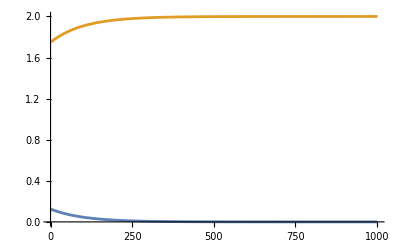
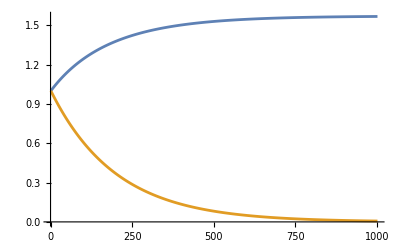

```mathematica
Planare2dofIK[0,2]
```

## Cartesiano 3DoF (PPP):

```mathematica
Cartesiano3dofITD[{qq1_,qq2_,qq3_},x_,y_,z_]:=Module[{hx,hy,hz,JJ,hh,p,ll,F,q1,q2,q3,T},
(*Verifico parametri*)
If[ListQ[qq1]!=False,Print["The argument 1 must be a scalar" ];Return[Null]];
If[ListQ[qq2]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];
If[ListQ[qq3]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];

If[ListQ[x]!=False,Print["The argument 3 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 4 must be a scalar" ];Return[Null]];
If[ListQ[z]!=False,Print["The argument 4 must be a scalar" ];Return[Null]];

T=0.01;
ll=1;
hx=q1;
hy=q2;
hz=q3;

JJ={{D[hx,q1],D[hx,q2], D[hx,q3]},
{D[hy,q1],D[hy,q2], D[hy,q3]},
{D[hz,q1],D[hz,q2], D[hz,q3]}} ;

hh={{hx},{hy},{hz}} ;
p={{x},{y},{z}} ;

F={{q1},{q2},{q3}}+T*ll*Inverse[JJ].(p-hh) /. {q1->qq1,q2->qq2,q3->qq3} ;
Flatten[F]
]
```

```mathematica
Cartesiano3dofIK[x_,y_,z_]:=Module[{s,n,q1,q2,q3,xx,yy,zz},
(*Verifico parametri*)
If[ListQ[x]!=False,Print["The argument 1 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];

Subscript[s, 0]={0,0,0};
n=1000;
Do[Subscript[s, i]=Cartesiano3dofITD[Subscript[s, i-1],x,y,z],{i,1,n}];

q1=Table[Subscript[s, i][[1]],{i,0,n}];
q2=Table[Subscript[s, i][[2]],{i,0,n}];
q3=Table[Subscript[s, i][[3]],{i,0,n}];
xx=q1;
yy=q2;
zz=q3;
{ListLinePlot[{xx,yy,zz},PlotRange->All], ListLinePlot[{q1,q2,q3},PlotRange->All]}
]
```

### test:

```mathematica
Cartesiano3dofITD[{1,1,1},1,1,1]
```

{1.,1.,1.}

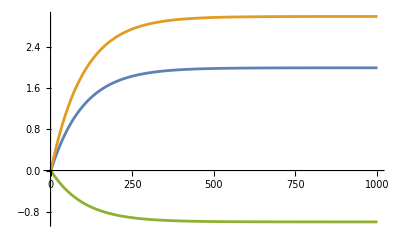
{-Graphics-,-Graphics-}

```mathematica
Cartesiano3dofIK[2,3,-1]
```

## Cilindrico 3DoF (RPP):

```mathematica
Cilindrico3dofITD[{qq1_,qq2_,qq3_},x_,y_,z_]:=Module[{hx,hy,hz,JJ,hh,p,ll,F,q1,q2,q3,T,D1},
(*Verifico parametri*)
If[ListQ[qq1]!=False,Print["The argument 1 must be a scalar" ];Return[Null]];
If[ListQ[qq2]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];
If[ListQ[qq3]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];

If[ListQ[x]!=False,Print["The argument 3 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 4 must be a scalar" ];Return[Null]];
If[ListQ[z]!=False,Print["The argument 4 must be a scalar" ];Return[Null]];

T=0.01;
ll=1;
D1=1;

hx=-q3*Sin[q1];
hy=q3*Cos[q1];
hz=D1+q2;

JJ={{D[hx,q1],D[hx,q2], D[hx,q3]},
{D[hy,q1],D[hy,q2], D[hy,q3]},
{D[hz,q1],D[hz,q2], D[hz,q3]}} ;

hh={{hx},{hy},{hz}} ;
p={{x},{y},{z}} ;

F={{q1},{q2},{q3}}+T*ll*Inverse[JJ].(p-hh) /. {q1->qq1,q2->qq2,q3->qq3} ;
Flatten[F]
]
```

```mathematica
Cilindrico3dofIK[x_,y_,z_]:=Module[{s,n,q1,q2,q3,xx,yy,zz},
(*Verifico parametri*)
If[ListQ[x]!=False,Print["The argument 1 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];

Subscript[s, 0]={1,1,1};
n=1000;
Do[Subscript[s, i]=Cilindrico3dofITD[Subscript[s, i-1],x,y,z],{i,1,n}];

q1=Table[Subscript[s, i][[1]],{i,0,n}];
q2=Table[Subscript[s, i][[2]],{i,0,n}];
q3=Table[Subscript[s, i][[3]],{i,0,n}];
xx=-q3*Sin[q1];
yy=q3*Cos[q1];
zz=1+q2;
{ListLinePlot[{xx,yy,zz},PlotRange->All], ListLinePlot[{q1,q2,q3},PlotRange->All]}
]
```

### test:

```mathematica
Cilindrico3dofITD[{1,2,3},4,5,6]
```

{0.978771,2.03,2.96336}

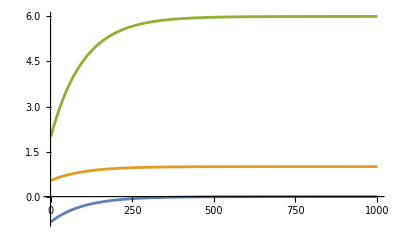
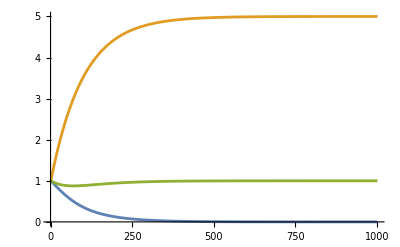

```mathematica
Cilindrico3dofIK[0,1,6]
```

## Scara 3 DoF (RRP):

```mathematica
Scara3dofITD[{qq1_,qq2_,qq3_},x_,y_,z_]:=Module[{hx,hy,hz,JJ,hh,p,ll,F,q1,q2,q3,T,D1,D2,L1,L2},
(*Verifico parametri*)
If[ListQ[qq1]!=False,Print["The argument 1 must be a scalar" ];Return[Null]];
If[ListQ[qq2]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];
If[ListQ[qq3]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];

If[ListQ[x]!=False,Print["The argument 3 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 4 must be a scalar" ];Return[Null]];
If[ListQ[z]!=False,Print["The argument 4 must be a scalar" ];Return[Null]];

T=0.01;
ll=1;
D1=1;
D2=1;
L1=1;
L2=1;

hx=L1*Cos[q1]+L2*Cos[q1+q2];
hy=L1*Sin[q1]+L2*Sin[q1+q2];
hz=D1+D2+q3;

JJ={{D[hx,q1],D[hx,q2], D[hx,q3]},
{D[hy,q1],D[hy,q2], D[hy,q3]},
{D[hz,q1],D[hz,q2], D[hz,q3]}} ;

hh={{hx},{hy},{hz}} ;
p={{x},{y},{z}} ;

F={{q1},{q2},{q3}}+T*ll*Inverse[JJ].(p-hh) /. {q1->qq1,q2->qq2,q3->qq3} ;
Flatten[F]
]
```

```mathematica
Scara3dofIK[x_,y_,z_]:=Module[{s,n,q1,q2,q3,xx,yy,zz},
(*Verifico parametri*)
If[ListQ[x]!=False,Print["The argument 1 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];

Subscript[s, 0]={1,1,1};
n=1000;
Do[Subscript[s, i]=Scara3dofITD[Subscript[s, i-1],x,y,z],{i,1,n}];

q1=Table[Subscript[s, i][[1]],{i,0,n}];
q2=Table[Subscript[s, i][[2]],{i,0,n}];
q3=Table[Subscript[s, i][[3]],{i,0,n}];
xx=Cos[q1]+Cos[q1+q2];
yy=Sin[q1]+Sin[q1+q2];
zz=2+q3;
{ListLinePlot[{xx,yy,zz},PlotRange->All], ListLinePlot[{q1,q2,q3},PlotRange->All]}
]
```

### test:

```mathematica
Scara3dofITD[{1,2,3},4,5,6]
```

{0.957789,1.97859,3.01}

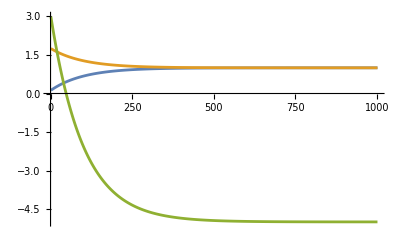
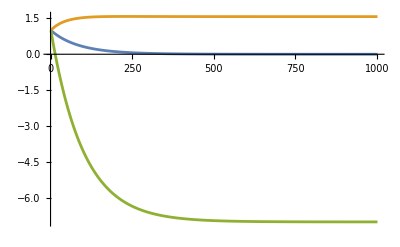

```mathematica
Scara3dofIK[1,1,-5]
```

## Sferico di 1° tipo 3 DoF (RRP):

```mathematica
Sferico1Tipo3dofITD[{qq1_,qq2_,qq3_},x_,y_,z_]:=Module[{hx,hy,hz,JJ,hh,p,ll,F,q1,q2,q3,T,D1,L2},
(*Verifico parametri*)
If[ListQ[qq1]!=False,Print["The argument 1 must be a scalar" ];Return[Null]];
If[ListQ[qq2]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];
If[ListQ[qq3]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];

If[ListQ[x]!=False,Print["The argument 3 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 4 must be a scalar" ];Return[Null]];
If[ListQ[z]!=False,Print["The argument 4 must be a scalar" ];Return[Null]];

T=0.01;
ll=1;
D1=1;
L2=1;

hx=(L2*Cos[q2]+q3*Sin[q2])*Cos[q1];
hy=(L2*Cos[q2]+q3*Sin[q2])*Sin[q1];
hz=L2*Sin[q2]-q3*Cos[q2]+D1;

JJ={{D[hx,q1],D[hx,q2], D[hx,q3]},
{D[hy,q1],D[hy,q2], D[hy,q3]},
{D[hz,q1],D[hz,q2], D[hz,q3]}} ;

hh={{hx},{hy},{hz}} ;
p={{x},{y},{z}} ;

F={{q1},{q2},{q3}}+T*ll*Inverse[JJ].(p-hh) /. {q1->qq1,q2->qq2,q3->qq3} ;
Flatten[F]
]
```

```mathematica
Sferico1Tipo3dofIK[x_,y_,z_]:=Module[{s,n,q1,q2,q3,xx,yy,zz},
(*Verifico parametri*)
If[ListQ[x]!=False,Print["The argument 1 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];

Subscript[s, 0]={1,1,1};
n=1000;
Do[Subscript[s, i]=Sferico1Tipo3dofITD[Subscript[s, i-1],x,y,z],{i,1,n}];

q1=Table[Subscript[s, i][[1]],{i,0,n}];
q2=Table[Subscript[s, i][[2]],{i,0,n}];
q3=Table[Subscript[s, i][[3]],{i,0,n}];
xx=(Cos[q2]+q3*Sin[q2])*Cos[q1];
yy=(Cos[q2]+q3*Sin[q2])*Sin[q1];
zz=Sin[q2]-q3*Cos[q2]+1;
{ListLinePlot[{xx,yy,zz},PlotRange->All], ListLinePlot[{q1,q2,q3},PlotRange->All]}
]
```

### test:

```mathematica
Sferico1Tipo3dofITD[{1,2,3},4,5,6]
```

{0.997126,2.00299,3.0517}

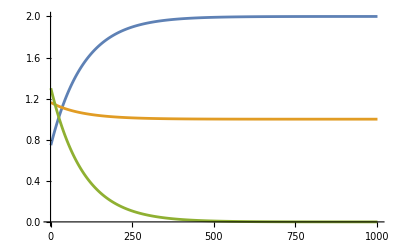
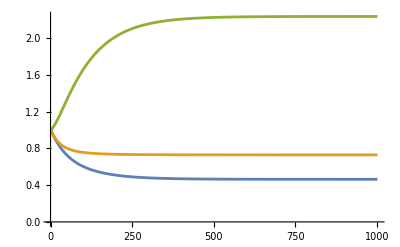

```mathematica
Sferico1Tipo3dofIK[2,1,0]
```

## Sferico Standford 3 DoF (RRP):

```mathematica
SfericoStandford3dofITD[{qq1_,qq2_,qq3_},x_,y_,z_]:=Module[{hx,hy,hz,JJ,hh,p,ll,F,q1,q2,q3,T,D1,D2},
(*Verifico parametri*)
If[ListQ[qq1]!=False,Print["The argument 1 must be a scalar" ];Return[Null]];
If[ListQ[qq2]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];
If[ListQ[qq3]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];

If[ListQ[x]!=False,Print["The argument 3 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 4 must be a scalar" ];Return[Null]];
If[ListQ[z]!=False,Print["The argument 4 must be a scalar" ];Return[Null]];

T=0.01;
ll=1;
D1=1;
D2=1;

hx=q3*Cos[q1]*Sin[q2]-D2*Sin[q1];
hy=q3*Sin[q1]*Sin[q2]+D2*Cos[q1];
hz=q3*Cos[q2]+D1;

JJ={{D[hx,q1],D[hx,q2], D[hx,q3]},
{D[hy,q1],D[hy,q2], D[hy,q3]},
{D[hz,q1],D[hz,q2], D[hz,q3]}} ;

hh={{hx},{hy},{hz}} ;
p={{x},{y},{z}} ;

F={{q1},{q2},{q3}}+T*ll*Inverse[JJ].(p-hh) /. {q1->qq1,q2->qq2,q3->qq3} ;
Flatten[F]
]
```

```mathematica
SfericoStandford3dofIK[x_,y_,z_]:=Module[{s,n,q1,q2,q3,xx,yy,zz},
(*Verifico parametri*)
If[ListQ[x]!=False,Print["The argument 1 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];

Subscript[s, 0]={1,1,1};
n=1000;
Do[Subscript[s, i]=SfericoStandford3dofITD[Subscript[s, i-1],x,y,z],{i,1,n}];

q1=Table[Subscript[s, i][[1]],{i,0,n}];
q2=Table[Subscript[s, i][[2]],{i,0,n}];
q3=Table[Subscript[s, i][[3]],{i,0,n}];

xx=q3*Cos[q1]*Sin[q2]-Sin[q1];
yy=q3*Sin[q1]*Sin[q2]+Cos[q1];
zz=q3*Cos[q2]+1;

{ListLinePlot[{xx,yy,zz},PlotRange->All], ListLinePlot[{q1,q2,q3},PlotRange->All]}
]
```

### test:

```mathematica
SfericoStandford3dofITD[{1,2,3},4,5,6]
```

{0.993899,1.97686,3.00155}

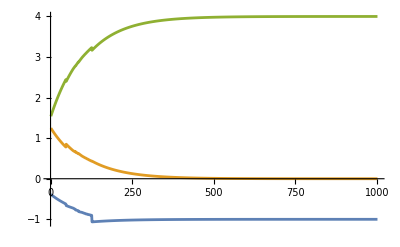
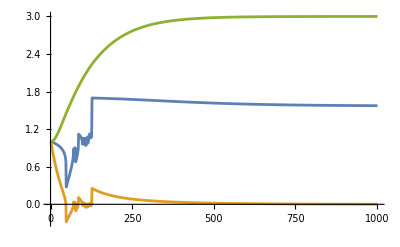

```mathematica
SfericoStandford3dofIK[-1,0,4]
```

## Antropomorfo 3 DoF (RRR):

```mathematica
Antropomorfo3dofITD[{qq1_,qq2_,qq3_},x_,y_,z_]:=Module[{hx,hy,hz,JJ,hh,p,ll,F,q1,q2,q3,T,D1,L1,L2,L3},
(*Verifico parametri*)
If[ListQ[qq1]!=False,Print["The argument 1 must be a scalar" ];Return[Null]];
If[ListQ[qq2]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];
If[ListQ[qq3]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];

If[ListQ[x]!=False,Print["The argument 3 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 4 must be a scalar" ];Return[Null]];
If[ListQ[z]!=False,Print["The argument 4 must be a scalar" ];Return[Null]];

T=0.01;
ll=1;
D1=1;
L1=1;
L2=1;
L3=1;

hx=Cos[q1]*(L1+L2*Cos[q2]+L3*Cos[q2+q3]);
hy=Sin[q1]*(L1+L2*Cos[q2]+L3*Cos[q2+q3]);
hz=D1+L2*Sin[q2]+L3*Sin[q2+q3];

JJ={{D[hx,q1],D[hx,q2], D[hx,q3]},
{D[hy,q1],D[hy,q2], D[hy,q3]},
{D[hz,q1],D[hz,q2], D[hz,q3]}} ;

hh={{hx},{hy},{hz}} ;
p={{x},{y},{z}} ;

F={{q1},{q2},{q3}}+T*ll*Inverse[JJ].(p-hh) /. {q1->qq1,q2->qq2,q3->qq3} ;
Flatten[F]
]
```

```mathematica
Antropomorfo3dofIK[x_,y_,z_]:=Module[{s,n,q1,q2,q3,xx,yy,zz},
(*Verifico parametri*)
If[ListQ[x]!=False,Print["The argument 1 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];

Subscript[s, 0]={1,1,1};
n=1000;
Do[Subscript[s, i]=Antropomorfo3dofITD[Subscript[s, i-1],x,y,z],{i,1,n}];

q1=Table[Subscript[s, i][[1]],{i,0,n}];
q2=Table[Subscript[s, i][[2]],{i,0,n}];
q3=Table[Subscript[s, i][[3]],{i,0,n}];

xx=Cos[q1]*(1+Cos[q2]+Cos[q2+q3]);
yy=Sin[q1]*(1+Cos[q2]+Cos[q2+q3]);
zz=1+Sin[q2]+Sin[q2+q3];

{ListLinePlot[{xx,yy,zz},PlotRange->All], ListLinePlot[{q1,q2,q3},PlotRange->All]}
]
```

### test:

```mathematica
Antropomorfo3dofITD[{1,2,3},4,5,6]
```

{0.992342,1.76745,3.0694}

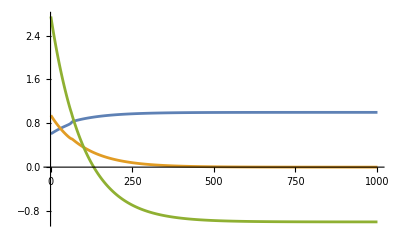
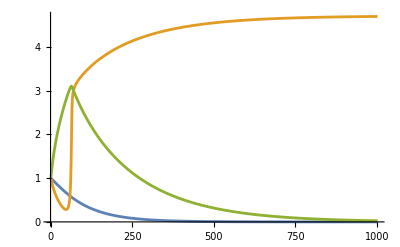

```mathematica
Antropomorfo3dofIK[1,0,-1]
```

## Polso Sferico 3 DoF (RRR):

```mathematica
PolsoSferico3dofITD[{qq1_,qq2_},x_,y_,z_]:=Module[{hx,hy,hz,JJ,hh,p,ll,F,q1,q2,q3,T,D1,D3},
(*Verifico parametri*)
If[ListQ[qq1]!=False,Print["The argument 1 must be a scalar" ];Return[Null]];
If[ListQ[qq2]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];

If[ListQ[x]!=False,Print["The argument 3 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 4 must be a scalar" ];Return[Null]];
If[ListQ[z]!=False,Print["The argument 4 must be a scalar" ];Return[Null]];

T=0.01;
ll=1;
D1=1;
D3=1;

(*notare che non abbiamo q3*)
hx=Cos[q1]*Sin[q2]*D3;
hy=Sin[q1]*Sin[q2]*D3;
hz=D1+D3*Cos[q2];

JJ={{D[hx,q1],D[hx,q2]},
{D[hy,q1],D[hy,q2]},
{D[hz,q1],D[hz,q2]}} ;

hh={{hx},{hy},{hz}} ;
p={{x},{y},{z}} ;

(*scegliamo q3 == 0 in maniera arbitraria e invece che Inverse[JJ] dobbiamo fare Transpose[JJ]*)
F={{q1},{q2}}+T*ll*Transpose[JJ].(p-hh) /. {q1->qq1,q2->qq2} ;
F=Flatten[F];
{F[[1]],F[[2]]}
]
```

```mathematica
PolsoSferico3dofIK[x_,y_,z_]:=Module[{s,n,q1,q2,xx,yy,zz},
(*Verifico parametri*)
If[ListQ[x]!=False,Print["The argument 1 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];

Subscript[s, 0]={1,1};
n=1000;
Do[Subscript[s, i]=PolsoSferico3dofITD[Subscript[s, i-1],x,y,z],{i,1,n}];

q1=Table[Subscript[s, i][[1]],{i,0,n}];
q2=Table[Subscript[s, i][[2]],{i,0,n}];

xx=Cos[q1]*Sin[q2];
yy=Sin[q1]*Sin[q2];
zz=1+Cos[q2];

{ListLinePlot[{xx,yy,zz},PlotRange->All], ListLinePlot[{q1,q2},PlotRange->All]}
]
```

### test:

```mathematica
PolsoSferico3dofITD[{1,2},4,5,6]
```

{0.993959,1.92803}

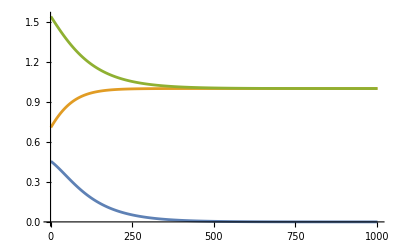
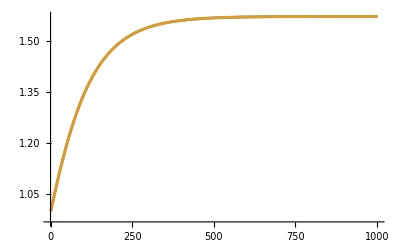

```mathematica
PolsoSferico3dofIK[0,1,1]
```

## Scorbot 5 DoF (RRR-RR):

```mathematica
Scorbot5dofITD[{qq1_,qq2_,qq3_,qq4_},x_,y_,z_]:=Module[{hx,hy,hz,JJ,hh,p,ll,F,q1,q2,q3,q4,T,D1,D5,L2,L3,L4},
(*Verifico parametri*)
If[ListQ[qq1]!=False,Print["The argument 1 must be a scalar" ];Return[Null]];
If[ListQ[qq2]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];
If[ListQ[qq3]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];
If[ListQ[qq4]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];

If[ListQ[x]!=False,Print["The argument 3 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 4 must be a scalar" ];Return[Null]];
If[ListQ[z]!=False,Print["The argument 4 must be a scalar" ];Return[Null]];

T=0.01;
ll=1;
D1=1;
D5=1;
L2=1;
L3=1;
L4=1;

hx=Cos[q1]*(Cos[q2]*L2+Cos[q2+q3]*L3+Cos[q2+q3+q4]*L4+D5*Sin[q2+q3+q4]);
hy=Sin[q1]*(Cos[q2]*L2+Cos[q2+q3]*L3+Cos[q2+q3+q4]*L4+D5*Sin[q2+q3+q4]);
hz=D1+Sin[q2]*L2+Sin[q2+q3]*L3+Sin[q2+q3+q4]*L4-D5*Cos[q2+q3+q4];

JJ={{D[hx,q1],D[hx,q2], D[hx,q3], D[hx,q4]},
{D[hy,q1],D[hy,q2], D[hy,q3], D[hy,q4]},
{D[hz,q1],D[hz,q2], D[hz,q3], D[hz,q4]}} ;

hh={{hx},{hy},{hz}} ;
p={{x},{y},{z}} ;

F={{q1},{q2},{q3},{q4}}+T*ll*Transpose[JJ].(p-hh) /. {q1->qq1,q2->qq2,q3->qq3,q4->qq4} ;
Flatten[F]
]
```

```mathematica
Scorbot5dofIK[x_,y_,z_]:=Module[{s,n,q1,q2,q3,q4,xx,yy,zz,D1,D5,L2,L3,L4},
(*Verifico parametri*)
If[ListQ[x]!=False,Print["The argument 1 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];

D1=1;
D5=1;
L2=1;
L3=1;
L4=1;

Subscript[s, 0]={1,1,1,1};
n=1000;
Do[Subscript[s, i]=Scorbot5dofITD[Subscript[s, i-1],x,y,z],{i,1,n}];

q1=Table[Subscript[s, i][[1]],{i,0,n}];
q2=Table[Subscript[s, i][[2]],{i,0,n}];
q3=Table[Subscript[s, i][[3]],{i,0,n}];
q4=Table[Subscript[s, i][[4]],{i,0,n}];

xx=Cos[q1]*(Cos[q2]*L2+Cos[q2+q3]*L3+Cos[q2+q3+q4]*L4+D5*Sin[q2+q3+q4]);
yy=Sin[q1]*(Cos[q2]*L2+Cos[q2+q3]*L3+Cos[q2+q3+q4]*L4+D5*Sin[q2+q3+q4]);
zz=D1+Sin[q2]*L2+Sin[q2+q3]*L3+Sin[q2+q3+q4]*L4-D5*Cos[q2+q3+q4];

{ListLinePlot[{xx,yy,zz},PlotRange->All], ListLinePlot[{q1,q2,q3,q4},PlotRange->All]}
]
```

### test:

```mathematica
Scorbot5dofITD[{1,2,3,4},1,1,1]
```

{1.0019,1.9824,2.99541,3.97971}

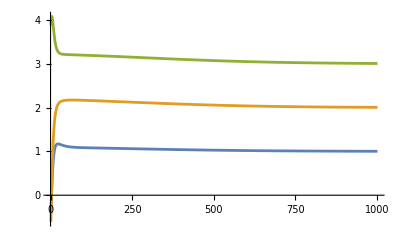
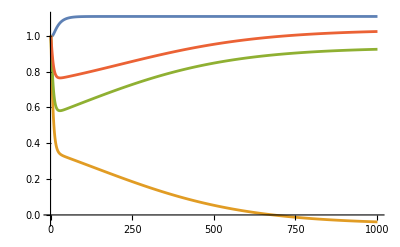

```mathematica
Scorbot5dofIK[1,2,3]
```

## Puma 6 DoF (RRR-RRR):

```mathematica
Puma6dofITD[{qq1_,qq2_,qq3_,qq4_,qq5_},x_,y_,z_]:=Module[{hx,hy,hz,JJ,hh,p,ll,F,q1,q2,q3,q4,q5,T,D1,D4,D6,L2},
(*Verifico parametri*)
If[ListQ[qq1]!=False,Print["The argument 1 must be a scalar" ];Return[Null]];
If[ListQ[qq2]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];
If[ListQ[qq3]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];
If[ListQ[qq4]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];
If[ListQ[qq5]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];

If[ListQ[x]!=False,Print["The argument 3 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 4 must be a scalar" ];Return[Null]];
If[ListQ[z]!=False,Print["The argument 4 must be a scalar" ];Return[Null]];

T=0.01;
ll=1;
D1=1;
D4=1;
D6=1;
L2=1;

hx=-D6*Sin[q1]*Sin[q4]*Sin[q5]+Cos[q1]*(Cos[q2]*L2+Cos[q2+q3]*D6*Sin[q5]+(D4+Cos[q5]*D6)*Sin[q2+q3]);
hy=Cos[q2]*L2*Sin[q1]+Cos[q1]*D6*Sin[q4]*Sin[q5]+Sin[q1]*(Cos[q3]*Cos[q2+q3]*D6*Sin[q5]+(D4+Cos[q5]*D6)*Sin[q2+q3]);
hz=D1+(D4+Cos[q5]*D6)*Cos[q2+q3]-L2*Sin[q2]-Cos[q3]*D6*Sin[q5]*Sin[q2+q3];

JJ={{D[hx,q1],D[hx,q2], D[hx,q3], D[hx,q4], D[hx,q5]},
{D[hy,q1],D[hy,q2], D[hy,q3], D[hy,q4], D[hy,q5]},
{D[hz,q1],D[hz,q2], D[hz,q3], D[hz,q4], D[hz,q5]}} ;

hh={{hx},{hy},{hz}} ;
p={{x},{y},{z}} ;

F={{q1},{q2},{q3},{q4},{q5}}+T*ll*Transpose[JJ].(p-hh) /. {q1->qq1,q2->qq2,q3->qq3,q4->qq4,q5->qq5} ;
Flatten[F]
]
```

```mathematica
Puma6dofIK[x_,y_,z_]:=Module[{s,n,q1,q2,q3,q4,q5,xx,yy,zz,D1,D4,D6,L2},
(*Verifico parametri*)
If[ListQ[x]!=False,Print["The argument 1 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];

D1=1;
D4=1;
D6=1;
L2=1;

Subscript[s, 0]={1,1,1,1,1};
n=1000;
Do[Subscript[s, i]=Puma6dofITD[Subscript[s, i-1],x,y,z],{i,1,n}];

q1=Table[Subscript[s, i][[1]],{i,0,n}];
q2=Table[Subscript[s, i][[2]],{i,0,n}];
q3=Table[Subscript[s, i][[3]],{i,0,n}];
q4=Table[Subscript[s, i][[4]],{i,0,n}];
q5=Table[Subscript[s, i][[5]],{i,0,n}];

xx=-D6*Sin[q1]*Sin[q4]*Sin[q5]+Cos[q1]*(Cos[q2]*L2+Cos[q2+q3]*D6*Sin[q5]+(D4+Cos[q5]*D6)*Sin[q2+q3]);
yy=Cos[q2]*L2*Sin[q1]+Cos[q1]*D6*Sin[q4]*Sin[q5]+Sin[q1]*(Cos[q3]*Cos[q2+q3]*D6*Sin[q5]+(D4+Cos[q5]*D6)*Sin[q2+q3]);
zz=D1+(D4+Cos[q5]*D6)*Cos[q2+q3]-L2*Sin[q2]-Cos[q3]*D6*Sin[q5]*Sin[q2+q3];

{ListLinePlot[{xx,yy,zz},PlotRange->All], ListLinePlot[{q1,q2,q3,q4,q5},PlotRange->All]}
]
```

### test:

```mathematica
Puma6dofITD[{1,2,3,4,5},1,1,1]
```

{1.00843,1.97945,3.00759,3.99202,4.97586}

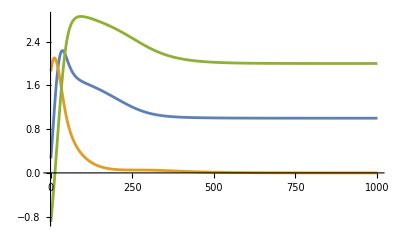
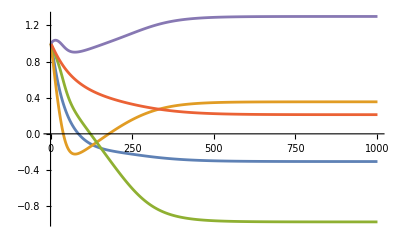

```mathematica
Puma6dofIK[1,0,2]
```

## Stanford 6 DoF (RRP-RRR):

```mathematica
Stanford6dofITD[{qq1_,qq2_,qq3_,qq4_,qq5_},x_,y_,z_]:=Module[{hx,hy,hz,JJ,hh,p,ll,F,q1,q2,q3,q4,q5,T,D1,D2,D6},
(*Verifico parametri*)
If[ListQ[qq1]!=False,Print["The argument 1 must be a scalar" ];Return[Null]];
If[ListQ[qq2]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];
If[ListQ[qq3]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];
If[ListQ[qq4]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];
If[ListQ[qq5]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];

If[ListQ[x]!=False,Print["The argument 3 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 4 must be a scalar" ];Return[Null]];
If[ListQ[z]!=False,Print["The argument 4 must be a scalar" ];Return[Null]];

T=0.01;
ll=1;
D1=1;
D2=1;
D6=1;

hx=Sin[q1]*(-D2+Cos[q3]*D6*Sin[q5])+Cos[q1]*((Cos[q5]*D6+q3)*Sin[q2]+Cos[q2]*D6*Sin[q4]*Sin[q5]);
hy=Cos[q1]*(D2-Cos[q3]*D6*Sin[q5])+Sin[q1]*((Cos[q5]*D6+q3)*Sin[q2]+Cos[q2]*D6*Sin[q4]*Sin[q5]);
hz=D1+Cos[q2]*(Cos[q5]*D6+q3)-D6*Sin[q2]*Sin[q4]*Sin[q5];

JJ={{D[hx,q1],D[hx,q2], D[hx,q3], D[hx,q4], D[hx,q5]},
{D[hy,q1],D[hy,q2], D[hy,q3], D[hy,q4], D[hy,q5]},
{D[hz,q1],D[hz,q2], D[hz,q3], D[hz,q4], D[hz,q5]}} ;

hh={{hx},{hy},{hz}} ;
p={{x},{y},{z}} ;

F={{q1},{q2},{q3},{q4},{q5}}+T*ll*Transpose[JJ].(p-hh) /. {q1->qq1,q2->qq2,q3->qq3,q4->qq4,q5->qq5} ;
Flatten[F]
]
```

```mathematica
Stanford6dofIK[x_,y_,z_]:=Module[{s,n,q1,q2,q3,q4,q5,xx,yy,zz,D1,D2,D6,L2},
(*Verifico parametri*)
If[ListQ[x]!=False,Print["The argument 1 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];
If[ListQ[y]!=False,Print["The argument 2 must be a scalar" ];Return[Null]];

D1=1;
D2=1;
D6=1;
L2=1;

Subscript[s, 0]={1,1,1,1,1};
n=1000;
Do[Subscript[s, i]=Stanford6dofITD[Subscript[s, i-1],x,y,z],{i,1,n}];

q1=Table[Subscript[s, i][[1]],{i,0,n}];
q2=Table[Subscript[s, i][[2]],{i,0,n}];
q3=Table[Subscript[s, i][[3]],{i,0,n}];
q4=Table[Subscript[s, i][[4]],{i,0,n}];
q5=Table[Subscript[s, i][[5]],{i,0,n}];

xx=Sin[q1]*(-D2+Cos[q3]*D6*Sin[q5])+Cos[q1]*((Cos[q5]*D6+q3)*Sin[q2]+Cos[q2]*D6*Sin[q4]*Sin[q5]);
yy=Cos[q1]*(D2-Cos[q3]*D6*Sin[q5])+Sin[q1]*((Cos[q5]*D6+q3)*Sin[q2]+Cos[q2]*D6*Sin[q4]*Sin[q5]);
zz=D1+Cos[q2]*(Cos[q5]*D6+q3)-D6*Sin[q2]*Sin[q4]*Sin[q5];

{ListLinePlot[{xx,yy,zz},PlotRange->All], ListLinePlot[{q1,q2,q3,q4,q5},PlotRange->All]}
]
```

### test:

```mathematica
Stanford6dofITD[{1,2,3,4,5},1,1,1]
```

{0.991217,1.972,2.9802,3.99185,4.98236}

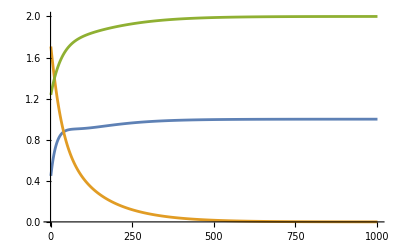
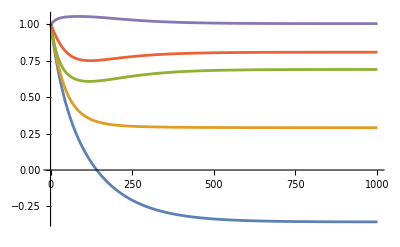

```mathematica
Stanford6dofIK[1,0,2]
```